## A366581: a(n) = phi(p(n)), where phi is Euler’s Totient function (A000010) and p(n) is the number of partitions of n (A000041).

### MATHEMATICA PROGRAM:

```mathematica
Table[EulerPhi[PartitionsP[n]],{n,0,48}] (*Paul F.Marrero Romero,Oct 14 2023*)
```

{1,1,1,2,4,6,10,8,10,8,12,24,60,100,72,80,120,180,240,168,360,240,332,1000,720,880,672,1008,1560,3280,1864,3100,4840,5544,4920,8800,17976,16800,18480,12960,10584,23040,24160,37800,57600,43440,34560,49896,84144}

### Formula:

a(n) = A000010(A000041(n)).

### Plot section:

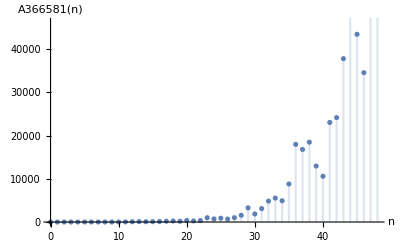

```mathematica
DiscretePlot[EulerPhi[PartitionsP[n]],{n,0,48}, AxesLabel->{"n", "A366581(n)"}, LabelStyle->Directive [Black, Bold]]
```

### References:

Sean A. Irvine, a(n) = phi(p(n)), where phi is Euler’s totient function (A000010) and p(n) is the number of partitions of n (A000041)., Entry A366581 in The On-Line Encyclopedia of Integer Sequences, https://oeis.org/A366581